### NHB paper Figure 3

```mathematica
(* Running the model for n=50 times per connection value
and 50,000 learning time steps each run *)

numRunsPerParam=50;
numLTimeSteps=500;
averIdStrengthsList={};
iGlobMax=7;

For[iGlob=0, iGlob≤iGlobMax, iGlob++,{
accStrengths=Array[0.0&,{nIdentity}];
For[iRun=1,iRun≤numRunsPerParam,iRun++,{
reInitialize[iGlob];
simulate[numLTimeSteps,nGlobal,nLocal];
accStrengths+=calculateAvStrengths[pop];
}];
AppendTo[averIdStrengthsList,accStrengths/numRunsPerParam];
}];
```

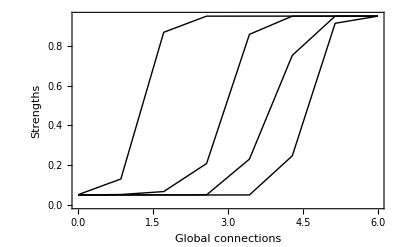

```mathematica
ListPlot[averIdStrengthsListᵀ,Joined->True, Frame->True,PlotRange-> Full,PlotStyle->{Array[Black&,{nIdentity}]},DataRange->{0,6},FrameLabel->{"Global connections","Strengths"}]
```

Simulation results used for Figure 3

```mathematica
averIdStrengthsListFig3={{0.0500202669300353,0.050099997892194416,0.05026108609011137,0.051382388705568806},{0.05013648693030518,0.050474812767317266,0.052401325971110024,0.1305680039845866},{0.05007781729250381,0.050541244044240666,0.06724455679266908,0.8686946445709853},{0.0501859435812362,0.050592723671159016,0.20825735273694052,0.9498820200376217},{0.05023166567700493,0.23049948505598253,0.8582482762892926,0.9500000000000006},{0.2469958039355215,0.7525186904223071,0.9500000000000006,0.9500000000000006},{0.9140048149382216,0.9500000000000006,0.9500000000000006,0.9500000000000006},{0.9500000000000006,0.9500000000000006,0.9500000000000006,0.9500000000000006},{0.9500000000000006,0.9500000000000006,0.9500000000000006,0.9500000000000006}};
```

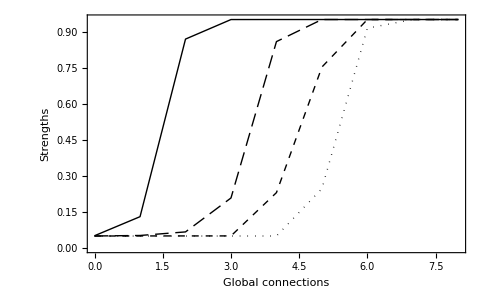

```mathematica
ListPlot[averIdStrengthsListFig3ᵀ,Joined->True, Frame->True,PlotRange-> Full,PlotStyle->{{Dotted,Black},{Dashed,Black},{Dashing[{0.02,0.01}],Black},Black},DataRange->{0,8},FrameLabel->{"Global connections","Strengths"},LabelStyle->Directive[14,FontFamily-> "Arial"]]
```